# Figure 1, Supplementary Table S1A, Supplementary Table S2A, Supplementary Table S3A

```mathematica
Clear["Global`*"]
```

```mathematica
data=Import[NotebookDirectory[]<>"nature25475-f1.xlsx","XLSX"]⟦1⟧;
```

```mathematica
data⟦1;;10⟧//TableForm
```

Subject | Gene | Qualifying Mutation | Allele/Domain | Bubble_Group | Tumor Type | Criteria | Percentage Change of Tumor Measurement | Best Overall Response | Progression-Free Survival Time (Months) | Ongoing
120. | ERBB2 | G778_P780dup | Exon20 Insertion Hotspot | Exon20 Insertion Hotspot | Breast | None | NA | SD | 20.0411 | NO
28. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | None | NA | PD | 1.34702 | NO
9. | ERBB2 | G776V  | PKD Hotspot | PKD Hotspot | Breast | None | NA | NONE | 4.3039 | NO
22. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | None | NA | PD | 0.952772 | NO
69. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | PERCIST | 31.3113 | PD | 1.70842 | NO
64. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | RECIST | 26.1053 | PD | 1.87269 | NO
66. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | RECIST | 2.54237 | PD | 1.80698 | NO
52. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | RECIST | 1.26582 | PD | 1.67556 | NO
71. | ERBB2 | L841V | Other Nonhotspot | PKD Nonhotspot | Breast | RECIST | 0. | SD | 2.75975 | NO

## analysis of all tumor types

```mathematica
AllVolumeChangeMeasurements=Select[data⟦2;;,8⟧,#≠"NA"&];
```

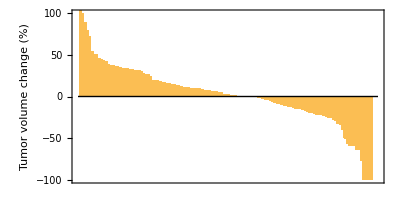

```mathematica
BarChart[Reverse[Sort[AllVolumeChangeMeasurements]],BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Black,Thickness[Medium]],PlotRange->{-100,100},PlotRangePadding->None,Frame->{{True,False},{False,False}},Axes->{True,False},AxesOrigin->{0,0},FrameLabel->{,"Tumor volume change (%)"},ImageSize->{{1000},{200}},AspectRatio->1/2]
```

```mathematica
Length[Select[AllVolumeChangeMeasurements,#<-30&]]/Length[AllVolumeChangeMeasurements]//N
```

0.12

```mathematica
RandomSamplePlot[samplesize_]:=BarChart[Reverse[Sort[RandomSample[Reverse[Sort[AllVolumeChangeMeasurements]],samplesize]]],BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Black,Thickness[Medium]],PlotRange->{-100,100},PlotRangePadding->None,Frame->{{True,False},{False,False}},Axes->{True,False},AxesOrigin->{0,0},(*FrameLabel->{,"Tumor volume change (%)"},*)AspectRatio->4,ImageSize->{{1000},{200}},ChartStyle->EdgeForm[None]]
```

```mathematica
VolumeChangeMeasurementsAndTumorType=Select[data⟦2;;,{6,8}⟧,#⟦2⟧≠"NA"&];
```

```mathematica
TumorTypes=Sort[Tally[VolumeChangeMeasurementsAndTumorType⟦All,1⟧],#1⟦2⟧>#2⟦2⟧&];
TumorTypes//TableForm
```

Lung | 21
Breast | 21
HER3_NOS | 15
Bladder | 15
Other | 14
Colorectal | 12
Biliary tract | 8
Endometrial | 7
Gastroesophageal | 5
Cervical | 4
Ovarian | 3

```mathematica
MeanResponsePerTumorType=Table[{TumorTypes⟦i,1⟧,Mean[Select[VolumeChangeMeasurementsAndTumorType,#⟦1⟧==TumorTypes⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[TumorTypes]}];
MeanResponsePerTumorType//TableForm
MedianResponsePerTumorType=Table[{TumorTypes⟦i,1⟧,Median[Select[VolumeChangeMeasurementsAndTumorType,#⟦1⟧==TumorTypes⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[TumorTypes]}];
MedianResponsePerTumorType//TableForm
```

Lung | -0.569079
Breast | -34.3426
HER3_NOS | 15.2358
Bladder | 13.1349
Other | 7.78957
Colorectal | 31.196
Biliary tract | -5.99053
Endometrial | 18.0495
Gastroesophageal | 25.9042
Cervical | -15.3244
Ovarian | 11.2802

Lung | 0.
Breast | -25.
HER3_NOS | 12.1951
Bladder | 17.7419
Other | 8.13118
Colorectal | 32.1596
Biliary tract | -6.47087
Endometrial | -9.2437
Gastroesophageal | 4.26829
Cervical | -17.7866
Ovarian | 6.66667

```mathematica
BreastAverageVolumeChange=Mean[Select[VolumeChangeMeasurementsAndTumorType,#⟦1⟧=="Breast"&]]⟦2⟧
NonBreastAverageVolumeChange=Mean[Select[VolumeChangeMeasurementsAndTumorType,#⟦1⟧!="Breast"&]]⟦2⟧

NonBreastAverageVolumeChange-BreastAverageVolumeChange
```

-34.3426

10.3606

44.7032

#### simulating null hypothesis

```mathematica
samplesize=10^7;
ManySamplesOfTrialMatchedSize=Table[
{TumorTypes⟦i,1⟧,Table[Mean[RandomSample[AllVolumeChangeMeasurements,TumorTypes⟦i,2⟧]],{samplesize}]}
,{i,1,Length[TumorTypes]}];
```

### Probability of larger benefit

```mathematica
PValuesByTumorType=Table[{TumorTypes⟦i,1⟧,Length[Select[ManySamplesOfTrialMatchedSize⟦i,2⟧,#<MeanResponsePerTumorType⟦i,2⟧&]]/samplesize//N},{i,1,11}]⟦{1,2,3,4,5,6,7,8,9,10,11}⟧
```

{{Lung,0.335439},{Breast,1.×10^-7},{HER3_NOS,0.901943},{Bladder,0.861776},{Other,0.701264},{Colorectal,0.992764},{Biliary tract,0.248959},{Endometrial,0.867562},{Gastroesophageal,0.919802},{Cervical,0.160612},{Ovarian,0.67453}}

```mathematica
SortedPValues=Join[{Range[11]},Sort[PValuesByTumorType,#1⟦2⟧<#2⟦2⟧&]ᵀ]ᵀ;
SortedPValues//TableForm
```

1 | Breast | 1.×10^-7
2 | Cervical | 0.160612
3 | Biliary tract | 0.248959
4 | Lung | 0.335439
5 | Ovarian | 0.67453
6 | Other | 0.701264
7 | Bladder | 0.861776
8 | Endometrial | 0.867562
9 | HER3_NOS | 0.901943
10 | Gastroesophageal | 0.919802
11 | Colorectal | 0.992764

### INCLUDING BREAST CANCER VOLUME CHANGES

```mathematica
Table[{SortedPValues⟦i,1⟧,SortedPValues⟦i,2⟧,SortedPValues⟦i,3⟧,(* benjamini-hochberg critical value: (i/m)*Q *)(SortedPValues⟦i,1⟧/Length[SortedPValues]*(* Q = 0.25 *)0.25//N)},{i,1,Length[SortedPValues]}]//TableForm
```

1 | Breast | 1.×10^-7 | 0.0227273
2 | Cervical | 0.160612 | 0.0454545
3 | Biliary tract | 0.248959 | 0.0681818
4 | Lung | 0.335439 | 0.0909091
5 | Ovarian | 0.67453 | 0.113636
6 | Other | 0.701264 | 0.136364
7 | Bladder | 0.861776 | 0.159091
8 | Endometrial | 0.867562 | 0.181818
9 | HER3_NOS | 0.901943 | 0.204545
10 | Gastroesophageal | 0.919802 | 0.227273
11 | Colorectal | 0.992764 | 0.25

```mathematica
ph (* plot height *)=0.06;

HistogramOfMeanResponseWithinATumorType[i_]:=Module[{},

myplot=Histogram[ManySamplesOfTrialMatchedSize⟦i,2⟧,{-50,60,1},"Probability",PlotLabel->Style[ManySamplesOfTrialMatchedSize⟦i,1⟧,Black,FontSize->11,FontFamily->"Arial"],PlotRange->{{-50,70},{0,ph}},PlotRangePadding->None,Frame->{{False,False},{True,False}},FrameStyle->Directive[Black,Thickness[Medium]],Epilog->{Red,AbsoluteThickness[2],Line[{{MeanResponsePerTumorType⟦i,2⟧,0},{MeanResponsePerTumorType⟦i,2⟧,ph}}]},ChartStyle->Directive[EdgeForm[None],Lighter[ColorData[3,6],0.5]],FrameTicks->{Join[Table[{j,j,{0,0.03}},{j,-100,100,20}](*,Table[{j,,{0,0.015}},{j,-100,100,10}]*)],None(*Join[Table[{j,100*j,{0,0.02}},{j,0,10/100,2/100}],Table[{j,,{0,0.01}},{j,0,10/100,2/100}]]*)},BaseStyle->{FontFamily->"Arial",FontSize->10},AspectRatio->0.3,ImagePadding->{{20,20},{40,5}},FrameLabel->{"Average tumor volume change (%)","Probability"},ImageSize->{{180},{300}}];

Export[NotebookDirectory[]<>"AverageVolumeByTumor - "<>ManySamplesOfTrialMatchedSize⟦i,1⟧<>".PDF", myplot,"PDF"];

myplot; 
]
HistogramOfMeanResponseWithinATumorType[2]
```

## Repeating the above, but leaving out breast cancer from the sample pool - because it is shown above to be clearly superior and not representative of the other tumor types’ responses.

```mathematica
AllVolumeChangeMeasurements=Select[data⟦2;;,{6,8}⟧,And[#⟦2⟧≠"NA",#⟦1⟧≠"Breast"]&]⟦All,2⟧;
AllVolumeChangeMeasurements//Length
```

104

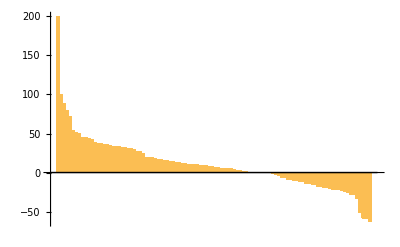

```mathematica
BarChart[Reverse[Sort[AllVolumeChangeMeasurements]]]
```

```mathematica
VolumeChangeMeasurementsAndTumorType=Select[data⟦2;;,{6,8}⟧,#⟦2⟧≠"NA"&];
```

```mathematica
TumorTypes=Sort[Tally[VolumeChangeMeasurementsAndTumorType⟦All,1⟧],#1⟦2⟧>#2⟦2⟧&];
TumorTypes//TableForm
```

Lung | 21
Breast | 21
HER3_NOS | 15
Bladder | 15
Other | 14
Colorectal | 12
Biliary tract | 8
Endometrial | 7
Gastroesophageal | 5
Cervical | 4
Ovarian | 3

```mathematica
MeanResponsePerTumorType=Table[{TumorTypes⟦i,1⟧,Mean[Select[VolumeChangeMeasurementsAndTumorType,#⟦1⟧==TumorTypes⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[TumorTypes]}];
MeanResponsePerTumorType//TableForm
MedianResponsePerTumorType=Table[{TumorTypes⟦i,1⟧,Median[Select[VolumeChangeMeasurementsAndTumorType,#⟦1⟧==TumorTypes⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[TumorTypes]}];
MedianResponsePerTumorType//TableForm
```

Lung | -0.569079
Breast | -34.3426
HER3_NOS | 15.2358
Bladder | 13.1349
Other | 7.78957
Colorectal | 31.196
Biliary tract | -5.99053
Endometrial | 18.0495
Gastroesophageal | 25.9042
Cervical | -15.3244
Ovarian | 11.2802

Lung | 0.
Breast | -25.
HER3_NOS | 12.1951
Bladder | 17.7419
Other | 8.13118
Colorectal | 32.1596
Biliary tract | -6.47087
Endometrial | -9.2437
Gastroesophageal | 4.26829
Cervical | -17.7866
Ovarian | 6.66667

```mathematica
samplesize=10^7;
ManySamplesOfTrialMatchedSize=Table[
{TumorTypes⟦i,1⟧,Table[Mean[RandomSample[AllVolumeChangeMeasurements,TumorTypes⟦i,2⟧]],{samplesize}]}
,{i,1,Length[TumorTypes]}];
```

```mathematica
ManySamplesOfTrialMatchedSize//Dimensions
```

{11,2}

```mathematica
ManySamplesOfTrialMatchedSize⟦1,1⟧
```

Lung

```mathematica
ph (* plot height *)=0.06;
HistogramOfMeanResponseWithinATumorType[i_]:=Module[{},

myplot=Histogram[ManySamplesOfTrialMatchedSize⟦i,2⟧,{-50,60,1},"Probability",PlotLabel->Style[ManySamplesOfTrialMatchedSize⟦i,1⟧,Black,FontSize->11,FontFamily->"Arial"],PlotRange->{{-50,70},{0,ph}},PlotRangePadding->None,Frame->{{False,False},{True,False}},FrameStyle->Directive[Black,Thickness[Medium]],Epilog->{Red,AbsoluteThickness[2],Line[{{MeanResponsePerTumorType⟦i,2⟧,0},{MeanResponsePerTumorType⟦i,2⟧,ph}}]},ChartStyle->Directive[EdgeForm[None],Lighter[ColorData[3,6],0.5]],FrameTicks->{Join[Table[{j,j,{0,0.03}},{j,-100,100,20}](*,Table[{j,,{0,0.015}},{j,-100,100,10}]*)],None(*Join[Table[{j,100*j,{0,0.02}},{j,0,10/100,2/100}],Table[{j,,{0,0.01}},{j,0,10/100,2/100}]]*)},BaseStyle->{FontFamily->"Arial",FontSize->10},AspectRatio->0.3,ImagePadding->{{20,20},{40,5}},FrameLabel->{"Average tumor volume change (%)","Probability"},ImageSize->{{180},{300}}];Export[NotebookDirectory[]<>"AverageVolumeByTumor, excluding Breast cancers - "<>ManySamplesOfTrialMatchedSize⟦i,1⟧<>".PDF", myplot,"PDF"];

myplot
]
```

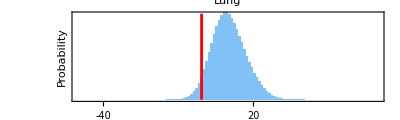

0.0398041

```mathematica
HistogramOfMeanResponseWithinATumorType[1]
(* P=value for being unusually ACTIVE *)
Length[Select[ManySamplesOfTrialMatchedSize⟦1,2⟧,#<MeanResponsePerTumorType⟦1,2⟧&]]/samplesize//N
```

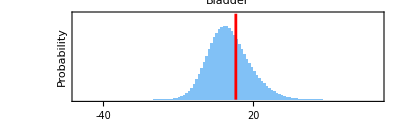

0.659163

```mathematica
HistogramOfMeanResponseWithinATumorType[4]
(* P=value for being unusually ACTIVE *)
Length[Select[ManySamplesOfTrialMatchedSize⟦4,2⟧,#<MeanResponsePerTumorType⟦4,2⟧&]]/samplesize//N
```

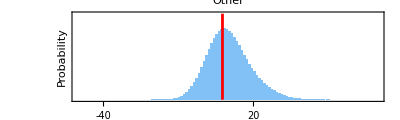

0.404189

```mathematica
HistogramOfMeanResponseWithinATumorType[5]
(* P=value for being unusually ACTIVE *)
Length[Select[ManySamplesOfTrialMatchedSize⟦5,2⟧,#<MeanResponsePerTumorType⟦5,2⟧&]]/samplesize//N
```

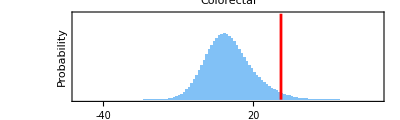

0.976957

```mathematica
HistogramOfMeanResponseWithinATumorType[6]
(* P=value for being unusually ACTIVE *)
Length[Select[ManySamplesOfTrialMatchedSize⟦6,2⟧,#<MeanResponsePerTumorType⟦6,2⟧&]]/samplesize//N
```

```mathematica
(* P-value for being unusually INACTIVE *)
Length[Select[ManySamplesOfTrialMatchedSize⟦6,2⟧,#>MeanResponsePerTumorType⟦6,2⟧&]]/samplesize//N
```

0.023043

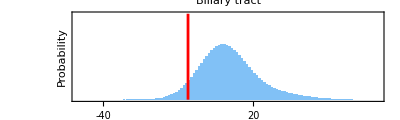

0.0590956

```mathematica
HistogramOfMeanResponseWithinATumorType[7]
(* P=value for being unusually ACTIVE *)
Length[Select[ManySamplesOfTrialMatchedSize⟦7,2⟧,#<MeanResponsePerTumorType⟦7,2⟧&]]/samplesize//N
```

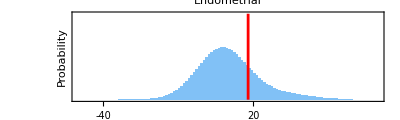

0.768385

```mathematica
HistogramOfMeanResponseWithinATumorType[8]
(* P=value for being unusually ACTIVE *)
Length[Select[ManySamplesOfTrialMatchedSize⟦8,2⟧,#<MeanResponsePerTumorType⟦8,2⟧&]]/samplesize//N
```

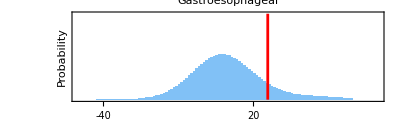

0.872518

```mathematica
HistogramOfMeanResponseWithinATumorType[9]
(* P=value for being unusually ACTIVE *)
Length[Select[ManySamplesOfTrialMatchedSize⟦9,2⟧,#<MeanResponsePerTumorType⟦9,2⟧&]]/samplesize//N
```

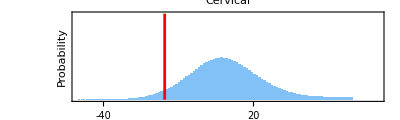

0.872518

```mathematica
HistogramOfMeanResponseWithinATumorType[10]
(* P=value for being unusually ACTIVE *)
Length[Select[ManySamplesOfTrialMatchedSize⟦9,2⟧,#<MeanResponsePerTumorType⟦9,2⟧&]]/samplesize//N
```

```mathematica
(* P=value for being unusually ACTIVE *)
Length[Select[ManySamplesOfTrialMatchedSize⟦10,2⟧,#<MeanResponsePerTumorType⟦10,2⟧&]]/samplesize//N
```

0.0387425

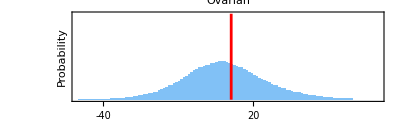

0.569025

```mathematica
HistogramOfMeanResponseWithinATumorType[11]
(* P=value for being unusually ACTIVE *)
Length[Select[ManySamplesOfTrialMatchedSize⟦11,2⟧,#<MeanResponsePerTumorType⟦11,2⟧&]]/samplesize//N
```

### Probability of larger benefit

```mathematica
PValuesByTumorType=Table[{TumorTypes⟦i,1⟧,Length[Select[ManySamplesOfTrialMatchedSize⟦i,2⟧,#<MeanResponsePerTumorType⟦i,2⟧&]]/samplesize//N},{i,1,11}]⟦{1,3,4,5,6,7,8,9,10,11}(* removing breast because it is such an outlier *)⟧
```

{{Lung,0.0398041},{HER3_NOS,0.742249},{Bladder,0.659163},{Other,0.404189},{Colorectal,0.976957},{Biliary tract,0.0590956},{Endometrial,0.768385},{Gastroesophageal,0.872518},{Cervical,0.0387425},{Ovarian,0.569025}}

```mathematica
SortedPValues=Join[{Range[10]},Sort[PValuesByTumorType,#1⟦2⟧<#2⟦2⟧&]ᵀ]ᵀ;
SortedPValues//TableForm
```

1 | Cervical | 0.0387425
2 | Lung | 0.0398041
3 | Biliary tract | 0.0590956
4 | Other | 0.404189
5 | Ovarian | 0.569025
6 | Bladder | 0.659163
7 | HER3_NOS | 0.742249
8 | Endometrial | 0.768385
9 | Gastroesophageal | 0.872518
10 | Colorectal | 0.976957

```mathematica
SortedPValuesForTissueTypes=SortedPValues⟦{1,2,3,5,6,8,9,10}⟧
```

{{1,Cervical,0.0387425},{2,Lung,0.0398041},{3,Biliary tract,0.0590956},{5,Ovarian,0.569025},{6,Bladder,0.659163},{8,Endometrial,0.768385},{9,Gastroesophageal,0.872518},{10,Colorectal,0.976957}}

#### one - sided test

```mathematica
Table[{SortedPValuesForTissueTypes⟦i,1⟧,SortedPValuesForTissueTypes⟦i,2⟧,SortedPValuesForTissueTypes⟦i,3⟧,(* benjamini-hochberg critical value: (i/m)*Q *)((i)/Length[SortedPValuesForTissueTypes]*(* Q = 0.25 *)0.25//N)},{i,1,Length[SortedPValuesForTissueTypes]}]//TableForm
Length[SortedPValuesForTissueTypes]
```

1 | Cervical | 0.0387425 | 0.03125
2 | Lung | 0.0398041 | 0.0625
3 | Biliary tract | 0.0590956 | 0.09375
5 | Ovarian | 0.569025 | 0.125
6 | Bladder | 0.659163 | 0.15625
8 | Endometrial | 0.768385 | 0.1875
9 | Gastroesophageal | 0.872518 | 0.21875
10 | Colorectal | 0.976957 | 0.25

8

## analysis of all MUTATIONS - simpler categories: hotspot VS non-hotspot ERBB2 vs ERBB3

```mathematica
AllVolumeChangeMeasurements=Select[data⟦2;;,8⟧,#≠"NA"&];
```

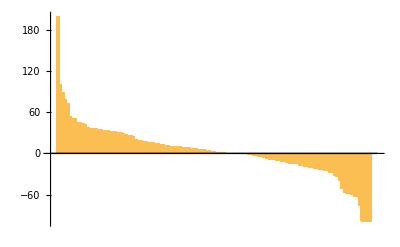

```mathematica
BarChart[Reverse[Sort[AllVolumeChangeMeasurements]]]
```

```mathematica
data⟦1;;10⟧//TableForm
```

Subject | Gene | Qualifying Mutation | Allele/Domain | Bubble_Group | Tumor Type | Criteria | Percentage Change of Tumor Measurement | Best Overall Response | Progression-Free Survival Time (Months) | Ongoing
120. | ERBB2 | G778_P780dup | Exon20 Insertion Hotspot | Exon20 Insertion Hotspot | Breast | None | NA | SD | 20.0411 | NO
28. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | None | NA | PD | 1.34702 | NO
9. | ERBB2 | G776V  | PKD Hotspot | PKD Hotspot | Breast | None | NA | NONE | 4.3039 | NO
22. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | None | NA | PD | 0.952772 | NO
69. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | PERCIST | 31.3113 | PD | 1.70842 | NO
64. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | RECIST | 26.1053 | PD | 1.87269 | NO
66. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | RECIST | 2.54237 | PD | 1.80698 | NO
52. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | RECIST | 1.26582 | PD | 1.67556 | NO
71. | ERBB2 | L841V | Other Nonhotspot | PKD Nonhotspot | Breast | RECIST | 0. | SD | 2.75975 | NO

```mathematica
Intersection[data⟦2;;,5⟧]
```

{ERBB3 Hotspot,ERBB3 Nonhotspot,Exon20 Insertion Hotspot,L755 Hotspot,Other Hotspot,Other Nonhotspot,PKD Hotspot,PKD Nonhotspot,S310 Hotspot,V777 Hotspot}

```mathematica
ERBB2hotspot={"Exon20 Insertion Hotspot","L755 Hotspot","Other Hotspot","PKD Hotspot","S310 Hotspot","V777 Hotspot"};
ERBB2nonhotspot={"Other Nonhotspot","PKD Nonhotspot"};
ERBB3hotspot={"ERBB3 Hotspot"};
ERBB3nonhotspot={"ERBB3 Nonhotspot"};
```

```mathematica
VolumeChangeMeasurementsAndMutationType=Select[data⟦2;;,{5,8}⟧,#⟦2⟧≠"NA"&];
```

```mathematica
MutationTypes=Sort[Tally[data⟦2;;,5⟧],#1⟦2⟧>#2⟦2⟧&];
MutationTypes//TableForm
```

S310 Hotspot | 30
Exon20 Insertion Hotspot | 28
V777 Hotspot | 15
PKD Hotspot | 14
L755 Hotspot | 13
ERBB3 Hotspot | 12
PKD Nonhotspot | 12
Other Hotspot | 9
ERBB3 Nonhotspot | 4
Other Nonhotspot | 4

```mathematica
ERBB2hotspotResponses=Select[VolumeChangeMeasurementsAndMutationType,MemberQ[ERBB2hotspot,#⟦1⟧]&];
ERBB2nonhotspotResponses=Select[VolumeChangeMeasurementsAndMutationType,MemberQ[ERBB2nonhotspot,#⟦1⟧]&];
ERBB3hotspotResponses=Select[VolumeChangeMeasurementsAndMutationType,MemberQ[ERBB3hotspot,#⟦1⟧]&];
ERBB3nonhotspotResponses=Select[VolumeChangeMeasurementsAndMutationType,MemberQ[ERBB3nonhotspot,#⟦1⟧]&];

TargetAndHotspotStratifiedResponses=Join[
Table[{"ERBB2 Hotspot",i⟦2⟧},{i,ERBB2hotspotResponses}],
Table[{"ERBB2 Nonhotspot",i⟦2⟧},{i,ERBB2nonhotspotResponses}],
Table[{"ERBB3 Hotspot",i⟦2⟧},{i,ERBB3hotspotResponses}],
Table[{"ERBB3 Nonhotspot",i⟦2⟧},{i,ERBB3nonhotspotResponses}]
];
```

```mathematica
(* OVERWRITING PREVIOUS MUTATIONTYPES DEFINITION *)
MutationTypes={
{"ERBB2 Hotspot","ERBB2 Nonhotspot","ERBB3 Hotspot","ERBB3 Nonhotspot"}
,
{Length[ERBB2hotspotResponses],Length[ERBB2nonhotspotResponses],Length[ERBB3hotspotResponses],Length[ERBB3nonhotspotResponses]}
}ᵀ;

MutationTypes//TableForm
```

ERBB2 Hotspot | 96
ERBB2 Nonhotspot | 14
ERBB3 Hotspot | 12
ERBB3 Nonhotspot | 3

```mathematica
MeanResponsePerMutationType=Table[{MutationTypes⟦i,1⟧,Mean[Select[TargetAndHotspotStratifiedResponses,#⟦1⟧==MutationTypes⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[MutationTypes]}];
MeanResponsePerMutationType//TableForm
MedianResponsePerMutationType=Table[{MutationTypes⟦i,1⟧,Median[Select[TargetAndHotspotStratifiedResponses,#⟦1⟧==MutationTypes⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[MutationTypes]}];
MedianResponsePerMutationType//TableForm
```

ERBB2 Hotspot | -0.843742
ERBB2 Nonhotspot | 14.9122
ERBB3 Hotspot | 19.1619
ERBB3 Nonhotspot | -0.468957

ERBB2 Hotspot | 0.
ERBB2 Nonhotspot | 12.7781
ERBB3 Hotspot | 15.6214
ERBB3 Nonhotspot | 6.97674

```mathematica
samplesize=10^7;
ManySamplesOfTrialMatchedSize=Table[
{MutationTypes⟦i,1⟧,Table[Mean[RandomSample[AllVolumeChangeMeasurements,MutationTypes⟦i,2⟧]],{samplesize}]}
,{i,1,Length[MutationTypes]}];
```

```mathematica
ManySamplesOfTrialMatchedSize//Dimensions
```

{4,2}

```mathematica
ManySamplesOfTrialMatchedSize⟦1,1⟧
```

ERBB2 Hotspot

```mathematica
HistogramOfMeanResponseWithinAMutationType[i_]:=Histogram[ManySamplesOfTrialMatchedSize⟦i,2⟧,{-50,50,1},"Probability",PlotLabel->ManySamplesOfTrialMatchedSize⟦i,1⟧,Epilog->{Red,AbsoluteThickness[2],Line[{{MeanResponsePerMutationType⟦i,2⟧,0},{MeanResponsePerMutationType⟦i,2⟧,0.1}}]}]


ph (* plot height *)=0.06;
(* simpler version for table - overwriting the previous definition *)
HistogramOfMeanResponseWithinAMutationType[i_]:=Module[{},

myplot=Histogram[ManySamplesOfTrialMatchedSize⟦i,2⟧,{-50,60,1},"Probability",PlotLabel->Style[ManySamplesOfTrialMatchedSize⟦i,1⟧,Black,FontSize->11,FontFamily->"Arial"],PlotRange->{{-50,70},{0,If[i==1,0.18,ph]}},PlotRangePadding->None,Frame->{{False,False},{True,False}},FrameStyle->Directive[Black,Thickness[Medium]],Epilog->{Red,AbsoluteThickness[2],Line[{{MeanResponsePerMutationType⟦i,2⟧,0},{MeanResponsePerMutationType⟦i,2⟧,If[i==1,0.2,ph]}}]},ChartStyle->Directive[EdgeForm[None],Lighter[ColorData[3,6],0.5]],FrameTicks->{Join[Table[{j,j,{0,0.05}},{j,-100,100,20}](*,Table[{j,,{0,0.015}},{j,-100,100,10}]*)],None(*Join[Table[{j,100*j,{0,0.02}},{j,0,10/100,2/100}],Table[{j,,{0,0.01}},{j,0,10/100,2/100}]]*)},BaseStyle->{FontFamily->"Arial",FontSize->10},AspectRatio->0.3,ImagePadding->{{20,20},{40,5}},FrameLabel->{"Average tumor volume change (%)","Probability"},ImageSize->{{180},{300}}];

Export[NotebookDirectory[]<>"AverageVolumeByMutation - "<>ManySamplesOfTrialMatchedSize⟦i,1⟧<>".PDF", myplot,"PDF"];

myplot
]
```

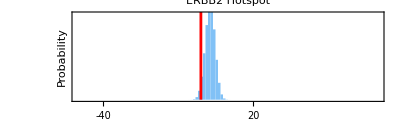

```mathematica
HistogramOfMeanResponseWithinAMutationType[1]
```

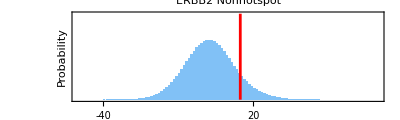

```mathematica
HistogramOfMeanResponseWithinAMutationType[2]
```

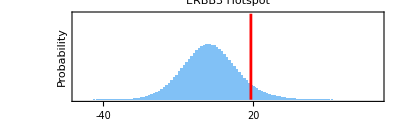

```mathematica
HistogramOfMeanResponseWithinAMutationType[3]
```

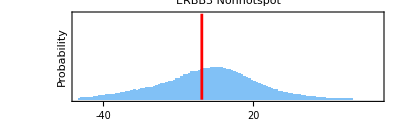

```mathematica
HistogramOfMeanResponseWithinAMutationType[4]
```

### Probability of larger benefit

```mathematica
PValuesByMutationType=Table[{MutationTypes⟦i,1⟧,Length[Select[ManySamplesOfTrialMatchedSize⟦i,2⟧,#<MeanResponsePerMutationType⟦i,2⟧&]]/samplesize//N},{i,1,Length[MeanResponsePerMutationType]}]
SortedPValues=Join[{Range[Length[MutationTypes]]},Sort[PValuesByMutationType,#1⟦2⟧<#2⟦2⟧&]ᵀ]ᵀ;
SortedPValues//TableForm

Table[{SortedPValues⟦i,1⟧,SortedPValues⟦i,2⟧,SortedPValues⟦i,3⟧,(* benjamini-hochberg critical value: (i/m)*Q *)(SortedPValues⟦i,1⟧/Length[SortedPValues]*(* Q = 0.25 *)0.25(*HALF FOR 2-SIDED TEST *)//N)},{i,1,Length[SortedPValues]}]//TableForm
```

{{ERBB2 Hotspot,0.0302088},{ERBB2 Nonhotspot,0.888417},{ERBB3 Hotspot,0.93132},{ERBB3 Nonhotspot,0.424382}}

1 | ERBB2 Hotspot | 0.0302088
2 | ERBB3 Nonhotspot | 0.424382
3 | ERBB2 Nonhotspot | 0.888417
4 | ERBB3 Hotspot | 0.93132

1 | ERBB2 Hotspot | 0.0302088 | 0.0625
2 | ERBB3 Nonhotspot | 0.424382 | 0.125
3 | ERBB2 Nonhotspot | 0.888417 | 0.1875
4 | ERBB3 Hotspot | 0.93132 | 0.25

## analysis of all MUTATIONS

```mathematica
AllVolumeChangeMeasurements=Select[data⟦2;;,8⟧,#≠"NA"&];
```

```mathematica
BarChart[Reverse[Sort[AllVolumeChangeMeasurements]]]
```

-Graphics-

```mathematica
data⟦1;;10⟧//TableForm
```

Subject | Gene | Qualifying Mutation | Allele/Domain | Bubble_Group | Tumor Type | Criteria | Percentage Change of Tumor Measurement | Best Overall Response | Progression-Free Survival Time (Months) | Ongoing
120. | ERBB2 | G778_P780dup | Exon20 Insertion Hotspot | Exon20 Insertion Hotspot | Breast | None | NA | SD | 20.0411 | NO
28. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | None | NA | PD | 1.34702 | NO
9. | ERBB2 | G776V  | PKD Hotspot | PKD Hotspot | Breast | None | NA | NONE | 4.3039 | NO
22. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | None | NA | PD | 0.952772 | NO
69. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | PERCIST | 31.3113 | PD | 1.70842 | NO
64. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | RECIST | 26.1053 | PD | 1.87269 | NO
66. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | RECIST | 2.54237 | PD | 1.80698 | NO
52. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | RECIST | 1.26582 | PD | 1.67556 | NO
71. | ERBB2 | L841V | Other Nonhotspot | PKD Nonhotspot | Breast | RECIST | 0. | SD | 2.75975 | NO

```mathematica
Intersection[data⟦2;;,5⟧]
```

{ERBB3 Hotspot,ERBB3 Nonhotspot,Exon20 Insertion Hotspot,L755 Hotspot,Other Hotspot,Other Nonhotspot,PKD Hotspot,PKD Nonhotspot,S310 Hotspot,V777 Hotspot}

```mathematica
VolumeChangeMeasurementsAndMutationType=Select[data⟦2;;,{5,8}⟧,#⟦2⟧≠"NA"&];
```

```mathematica
MutationTypes=Sort[Tally[data⟦2;;,5⟧],#1⟦2⟧>#2⟦2⟧&];
MutationTypes//TableForm
```

S310 Hotspot | 30
Exon20 Insertion Hotspot | 28
V777 Hotspot | 15
PKD Hotspot | 14
L755 Hotspot | 13
ERBB3 Hotspot | 12
PKD Nonhotspot | 12
Other Hotspot | 9
ERBB3 Nonhotspot | 4
Other Nonhotspot | 4

```mathematica
MeanResponsePerMutationType=Table[{MutationTypes⟦i,1⟧,Mean[Select[VolumeChangeMeasurementsAndMutationType,#⟦1⟧==MutationTypes⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[MutationTypes]}];
MeanResponsePerMutationType//TableForm
MedianResponsePerMutationType=Table[{MutationTypes⟦i,1⟧,Median[Select[VolumeChangeMeasurementsAndMutationType,#⟦1⟧==MutationTypes⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[MutationTypes]}];
MedianResponsePerMutationType//TableForm
```

S310 Hotspot | -1.10753
Exon20 Insertion Hotspot | -3.59641
V777 Hotspot | -2.83471
PKD Hotspot | 19.6223
L755 Hotspot | -15.9803
ERBB3 Hotspot | 19.1619
PKD Nonhotspot | 6.6781
Other Hotspot | 3.45044
ERBB3 Nonhotspot | -0.468957
Other Nonhotspot | 35.4973

S310 Hotspot | 2.02703
Exon20 Insertion Hotspot | 0.
V777 Hotspot | -0.929589
PKD Hotspot | 4.85714
L755 Hotspot | -3.46161
ERBB3 Hotspot | 15.6214
PKD Nonhotspot | 9.06649
Other Hotspot | -13.6185
ERBB3 Nonhotspot | 6.97674
Other Nonhotspot | 28.078

```mathematica
samplesize=10^7;
ManySamplesOfTrialMatchedSize=Table[
{MutationTypes⟦i,1⟧,Table[Mean[RandomSample[AllVolumeChangeMeasurements,MutationTypes⟦i,2⟧]],{samplesize}]}
,{i,1,Length[MutationTypes]}];
```

```mathematica
ManySamplesOfTrialMatchedSize//Dimensions
```

{10,2}

```mathematica
ManySamplesOfTrialMatchedSize⟦1,1⟧
```

S310 Hotspot

```mathematica
(* simpler version for table - overwriting the previous definition *)
HistogramOfMeanResponseWithinAMutationType[i_]:=Module[{},

myplot=Histogram[ManySamplesOfTrialMatchedSize⟦i,2⟧,{-50,60,1},"Probability",PlotLabel->Style[ManySamplesOfTrialMatchedSize⟦i,1⟧,Black,FontSize->11,FontFamily->"Arial"],PlotRange->{{-50,70},{0,ph}},PlotRangePadding->None,Frame->{{False,False},{True,False}},FrameStyle->Directive[Black,Thickness[Medium]],Epilog->{Red,AbsoluteThickness[2],Line[{{MeanResponsePerMutationType⟦i,2⟧,0},{MeanResponsePerMutationType⟦i,2⟧,ph}}]},ChartStyle->Directive[EdgeForm[None],Lighter[ColorData[3,6],0.5]],FrameTicks->{Join[Table[{j,j,{0,0.03}},{j,-100,100,20}](*,Table[{j,,{0,0.015}},{j,-100,100,10}]*)],None(*Join[Table[{j,100*j,{0,0.02}},{j,0,10/100,2/100}],Table[{j,,{0,0.01}},{j,0,10/100,2/100}]]*)},BaseStyle->{FontFamily->"Arial",FontSize->10},AspectRatio->0.3,ImagePadding->{{20,20},{40,5}},FrameLabel->{"Average tumor volume change (%)","Probability"},ImageSize->{{180},{300}}];

Export[NotebookDirectory[]<>"AverageVolumeByMutation - "<>ManySamplesOfTrialMatchedSize⟦i,1⟧<>".PDF", myplot,"PDF"];

myplot
]
```

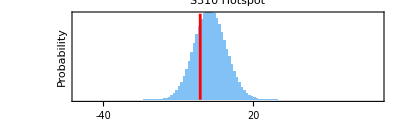

```mathematica
HistogramOfMeanResponseWithinAMutationType[1]
```

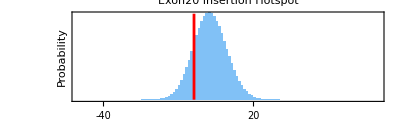

```mathematica
HistogramOfMeanResponseWithinAMutationType[2]
```

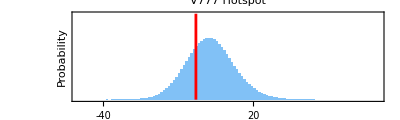

```mathematica
HistogramOfMeanResponseWithinAMutationType[3]
```

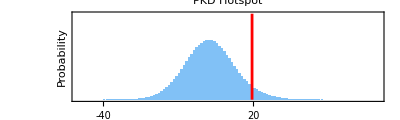

```mathematica
HistogramOfMeanResponseWithinAMutationType[4]
```

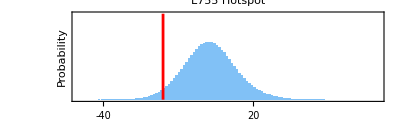

```mathematica
HistogramOfMeanResponseWithinAMutationType[5]
```

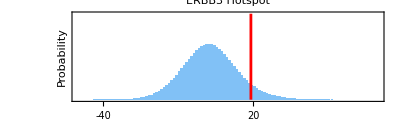

```mathematica
HistogramOfMeanResponseWithinAMutationType[6]
```

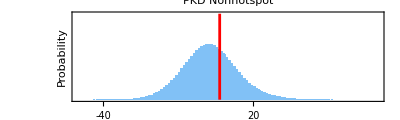

```mathematica
HistogramOfMeanResponseWithinAMutationType[7]
```

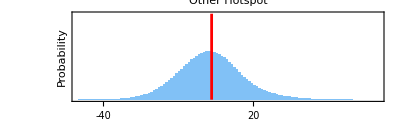

```mathematica
HistogramOfMeanResponseWithinAMutationType[8]
```

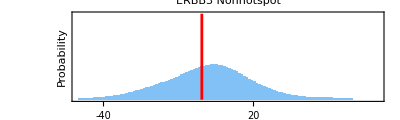

```mathematica
HistogramOfMeanResponseWithinAMutationType[9]
```

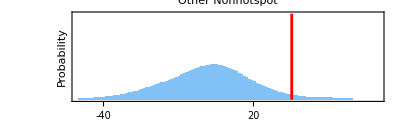

```mathematica
HistogramOfMeanResponseWithinAMutationType[10]
```

### Probability of larger benefit

```mathematica
PValuesByMutationType=Table[{MutationTypes⟦i,1⟧,Length[Select[ManySamplesOfTrialMatchedSize⟦i,2⟧,#<MeanResponsePerMutationType⟦i,2⟧&]]/samplesize//N},{i,1,Length[MeanResponsePerMutationType]}]
```

{{S310 Hotspot,0.267131},{Exon20 Insertion Hotspot,0.162915},{V777 Hotspot,0.275623},{PKD Hotspot,0.949998},{L755 Hotspot,0.0310298},{ERBB3 Hotspot,0.93151},{PKD Nonhotspot,0.651051},{Other Hotspot,0.52835},{ERBB3 Nonhotspot,0.421824},{Other Nonhotspot,0.954185}}

```mathematica
SortedPValues=Join[{Range[10]},Sort[PValuesByMutationType,#1⟦2⟧<#2⟦2⟧&]ᵀ]ᵀ;
SortedPValues//TableForm
```

1 | L755 Hotspot | 0.0310298
2 | Exon20 Insertion Hotspot | 0.162915
3 | S310 Hotspot | 0.267131
4 | V777 Hotspot | 0.275623
5 | ERBB3 Nonhotspot | 0.421824
6 | Other Hotspot | 0.52835
7 | PKD Nonhotspot | 0.651051
8 | ERBB3 Hotspot | 0.93151
9 | PKD Hotspot | 0.949998
10 | Other Nonhotspot | 0.954185

```mathematica
Table[{SortedPValues⟦i,1⟧,SortedPValues⟦i,2⟧,SortedPValues⟦i,3⟧,(* benjamini-hochberg critical value: (i/m)*Q *)(SortedPValues⟦i,1⟧/Length[SortedPValues]*(* Q = 0.25 *)0.25//N)},{i,1,Length[SortedPValues]}]//TableForm
```

1 | L755 Hotspot | 0.0310298 | 0.025
2 | Exon20 Insertion Hotspot | 0.162915 | 0.05
3 | S310 Hotspot | 0.267131 | 0.075
4 | V777 Hotspot | 0.275623 | 0.1
5 | ERBB3 Nonhotspot | 0.421824 | 0.125
6 | Other Hotspot | 0.52835 | 0.15
7 | PKD Nonhotspot | 0.651051 | 0.175
8 | ERBB3 Hotspot | 0.93151 | 0.2
9 | PKD Hotspot | 0.949998 | 0.225
10 | Other Nonhotspot | 0.954185 | 0.25